# 微积分

## 一阶偏导

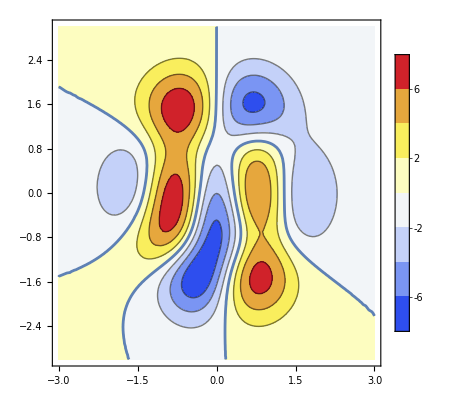
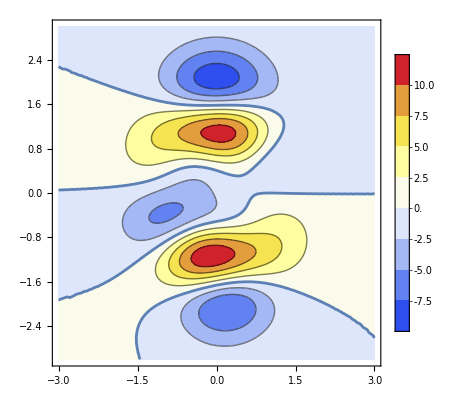

```mathematica
complexFunction[x1_,x2_]=3(1-x1)^2Exp[-x1^2-(x2+1)^2]-10(x1/5-x1^3-x2^5)Exp[-x1^2-x2^2]-1/3 Exp[-(x1+1)^2-x2^2];
dx1=D[complexFunction[x,y],x]; (*对x1求偏导*)
dx2=D[complexFunction[x,y],y];(*对x2求偏导*)
Show[ContourPlot[#,{x,-3,3},{y,-3,3},ColorFunction->"TemperatureMap",PlotTheme->"Detailed",PlotRange->All],ContourPlot[#==0,{x,-3,3},{y,-3,3}]]&/@{dx1,dx2}
```

## 二元函数的驻点

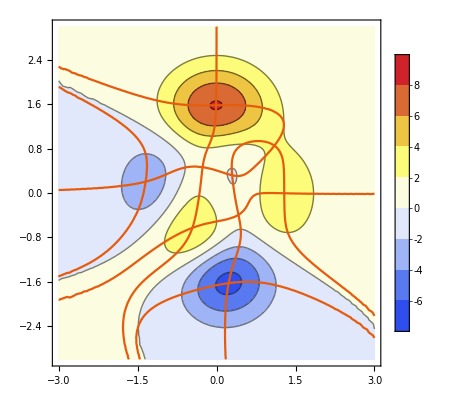

```mathematica
Show[ContourPlot[complexFunction[x,y],{x,-3,3},{y,-3,3},ColorFunction->"TemperatureMap",PlotTheme->"Detailed",PlotRange->All],ContourPlot[#==0,{x,-3,3},{y,-3,3},PlotTheme->"Scientific"]&/@{dx1,dx2}](*曲线交点为极值点或鞍点*)
```

## 二阶偏导

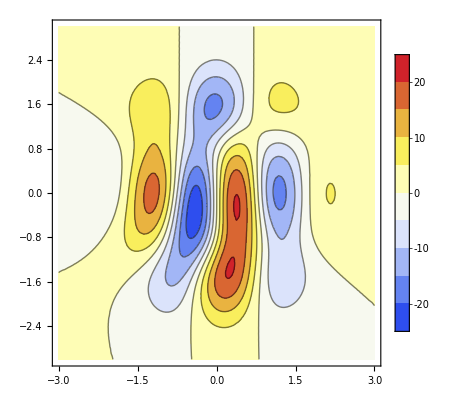
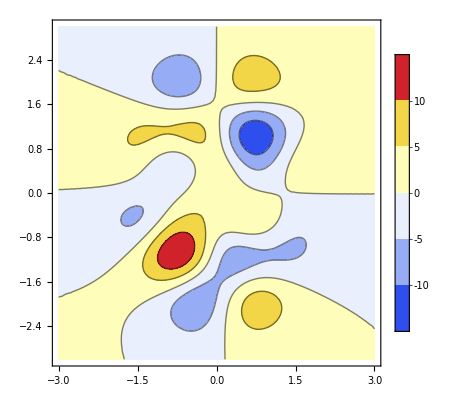
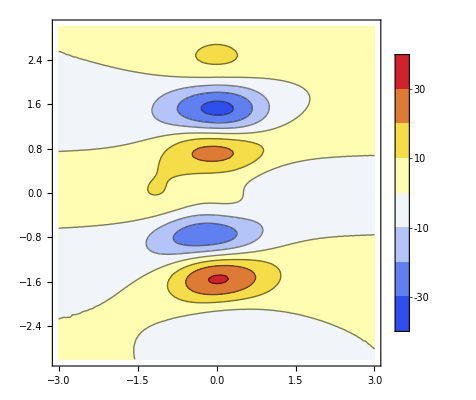

```mathematica
dx11=D[complexFunction[x,y],{x,2}];
dx12=D[complexFunction[x,y],x,y];
dx22=D[complexFunction[x,y],{y,2}];
ContourPlot[#,{x,-3,3},{y,-3,3},ColorFunction->"TemperatureMap",PlotTheme->"Detailed",PlotRange->All]&/@{dx11,dx12,dx22}
```

## 三种差分

```mathematica
numDiff[f_,a_,method_,dx_]:=Module[{result},Switch[method,"central",result=(f[a+dx]-f[a-dx])/(2*dx),"forward",result=(f[a+dx]-f[a])/dx,"backward",result=(f[a]-f[a-dx])/dx,_,Throw["Method must be 'central', 'forward' or 'backward'."];];
result]
```

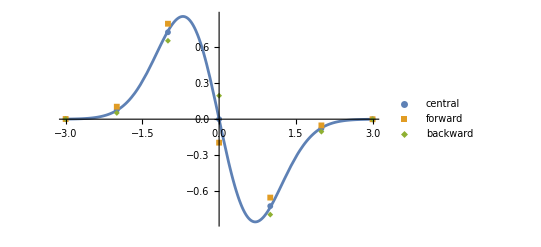

```mathematica
D[Exp[-x^2],x];
Show[Plot[%,{x,-3,3}],ListPlot[Table[{i,numDiff[Exp[-#^2]&,i,#,0.2]},{i,-3,3}]&/@{"central","forward","backward"},PlotLegends->{"central","forward","backward"},PlotMarkers->{Automatic, 6}]]
```

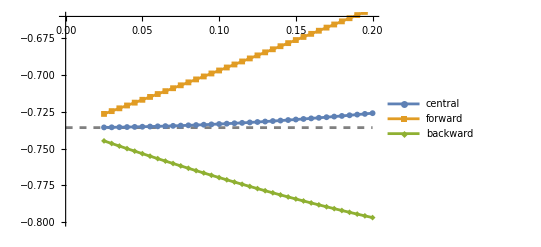

```mathematica
D[Exp[-x^2],x];
Show[Plot[%/.x->1,{i,0,.2},PlotRange->{-.8,-.66},PlotStyle->{Gray,Dashed}],ListLinePlot[Table[{i,numDiff[Exp[-#^2]&,1,#,i]},{i,0.025,0.2,0.005}]&/@{"central","forward","backward"},PlotMarkers->{Automatic, 6},PlotLegends->{"central","forward","backward"}]](*在x=1这一点，改变步长，看三种差分方法的误差大小*)
```

## 牛顿法估算圆周率 -Graphics-

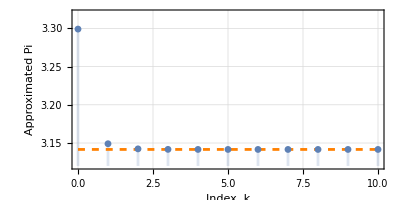

```mathematica
24(Sqrt[3]/32-Sum[((2k)!)/(2^(4k+2)(k!)^2(2k-1)(2k+3)),{k,0,n}]);
Show[DiscretePlot[%,{n,0,10},PlotRange->{3.12,3.32},AspectRatio->1/2,PlotMarkers->{Automatic,Small},GridLines->Automatic,Frame->True,FrameLabel->{"Index, k","Approximated Pi"}],Plot[Pi,{x,0,10},PlotStyle->{Orange,Dashed}]]
```

## 蒙特卡洛模拟估算圆周率

```mathematica
MonteCarloPi[n_]:=Module[{points,inCircle,estimatedPi,error},points=RandomReal[{-1,1},{n,2}];
inCircle=Select[points,Norm[#]<=1&];
estimatedPi=4 Length[inCircle]/Length[points];
error=Abs[N[Pi]-estimatedPi];
{estimatedPi,error}]
```

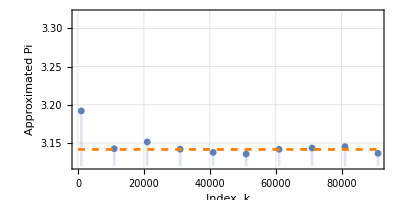

```mathematica
Show[DiscretePlot[MonteCarloPi[n][[1]],{n,1000,100000,10000},PlotRange->{3.12,3.32},AspectRatio->1/2,PlotMarkers->{Automatic,Small},GridLines->Automatic,Frame->True,FrameLabel->{"Index, k","Approximated Pi"}],Plot[Pi,{x,0,100000},PlotStyle->{Orange,Dashed}]]
```

```mathematica
MonteCarloPi[1000000];
Print["Estimated Pi: ",%[[1]],"\n","Error: ",error]
```

Estimated Pi: 392431/125000
Error: error

## 黎曼和

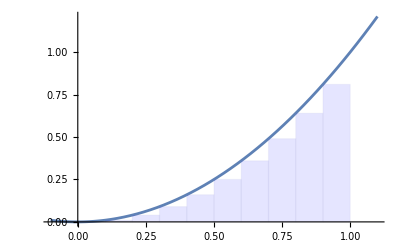
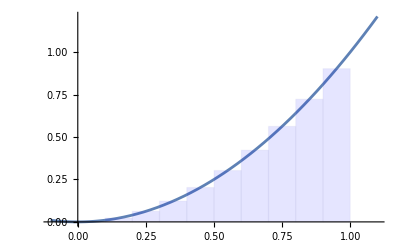
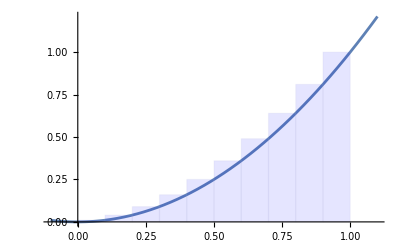
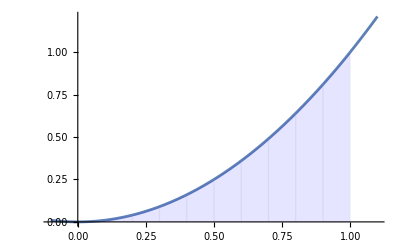
<|Left→-Graphics-,Midpoint→-Graphics-,Right→-Graphics-,Trapezoidal→-Graphics-|>

```mathematica
ResourceFunction["RiemannSum"][x^2,{x,0,1,10},All,"Plot"]
```

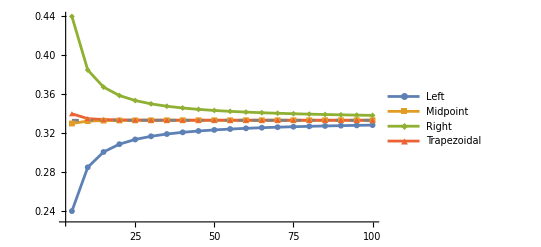

```mathematica
Show[ListLinePlot[Table[{n,N@ResourceFunction["RiemannSum"][x^2,{x,0,1,n},m,type,"Sum"]},{type,{"Left","Midpoint","Right","Trapezoidal"}},{n,5,100,5}],PlotMarkers->{Automatic, 6},PlotLegends->{"Left","Midpoint","Right","Trapezoidal"},PlotRange->All],Plot[1/3,{x,5,100},PlotStyle->{Gray,Dashed}]]
```